```mathematica
f = 16*^6;
fc = 17*^6;
rm = 100*^3 + ER;
ER = 6.371*^6;
rb = 50*^3 + ER;
ym = rm-rb;
CInput = (fc rb rm / (f ym))^2 - (ER Cos[beta0])^2;
a = 1 -(fc/f)^2 + (fc rb/ (f ym))^2;
b = -2 rm(fc rb/(f ym))^2;
BetaBInput = ArcCos[ER/rb Cos[beta0]];
XBInput = rb^2 -(ER Cos[beta0])^2;
mult = ER^2 * Cos[beta0]/Sqrt[c];
numerator = (2*c + b*rb + 2*Sqrt[c*xb]);
denominator = (rb * Sqrt[b^2 - 4*a*c]);
discriminant =b^2 - 4 a c;
XInput = a r^2 + b r + CInput;
distance = ER(BetaBInput - beta0) + ER^2 * Cos[beta0]/Sqrt[CInput]*Log[r(2*CInput + b*rb + 2*Sqrt[CInput*XBInput])/(rb (2CInput + r * b + 2Sqrt[CInput XInput]))];
```

```mathematica
ClearAll[fc, f, ER, rm, rb, beta];
```

```mathematica
(*Calculate Heights*)
MaxDistance[angle_]:=2(ER(BetaBInput - beta0) + ER^2Cos[beta0]/Sqrt[CInput]Log[(2CInput + b rb + 2Sqrt[CInput XBInput])/(rb Sqrt[b^2 - 4 a CInput])])/.beta0->angle;
UnifiedDistance[dist_, angle_]:=If[dist<MaxDistance[angle]/2,dist, MaxDistance[angle] - dist] ;
BelowAtmosphereHeight[dist_, angle_]:=ER * Cos[angle]/Cos[dist/ER + angle];
UTerm [dist_, angle_]:= Sqrt[CInput](dist - ER(BetaBInput - beta0))/(ER^2 Cos[beta0])/.beta0->angle;
VTerm[dist_, angle_]:=(2CInput + rb b + 2Sqrt[CInput XBInput])/(rb Exp[UTerm[dist, angle]])/.beta0->angle;
AboveAtmosphereHeight[dist_, angle_]:=4 VTerm[dist, angle] CInput /((VTerm[dist, angle] - b)^2 - 4 a CInput)/.beta0->angle;
currentAngle = π/4;
PenetrationDistance[angle_]:=ER(-beta0 + ArcCos[ER/rb Cos[beta0]])/.beta0->angle
Height[dist_,angle_]:=If[UnifiedDistance[dist, angle]<PenetrationDistance[angle], BelowAtmosphereHeight[UnifiedDistance[dist, angle], angle], AboveAtmosphereHeight[UnifiedDistance[dist, angle], angle]]
resultsVector = Table[{i/10*MaxDistance[currentAngle], Height[i/10*MaxDistance[currentAngle], currentAngle] - ER}, {i, 0, 10}];
results =Table[StringForm["``: ``",CForm[i/10*MaxDistance[currentAngle]], CForm[Height[i/10*MaxDistance[currentAngle], currentAngle] - ER]], {i, 0, 10}];
StandardForm[results]
```

{0.: -1.862645149230957e-9,15189.298426254249: 15243.777116704732,30378.596852508497: 30597.150661764666,45567.89527876274: 46061.088167474605,60757.193705016994: 58815.94639489055,75946.49213127124: 62896.03693717811,91135.79055752548: 58815.94639489055,106325.08898377973: 46061.088167474605,121514.38741003399: 30597.150661764666,136703.68583628823: 15243.777116704732,151892.98426254248: -1.862645149230957e-9}

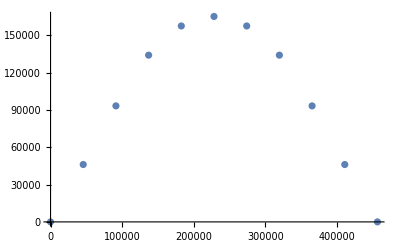

{{0.,-1.86265×10^-9},{45670.8,46166.2},{91341.6,93341.1},{137012.,134156.},{182683.,157652.},{228354.,165300.},{274025.,157652.},{319696.,134156.},{365366.,93341.1},{411037.,46166.2},{456708.,-1.86265×10^-9}}

```mathematica
ListPlot[resultsVector]
resultsVector
```

```mathematica
Angles = {
{0.7358512158582213,0.050458771311181365},
{0.6141922626335141,0.6137515419925214},
{0.24350740847807326}
};
Atmospheres = {
{6571000,6411000,607789630364.6737,10000000.0},
{6871000,6721000,607789630364.6737,10000000.0},
{6471000,6421000,3584718432150.831,16000000.0}
};
```